```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/LYE/GDC_Conf_AR_LYE_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/LYE/GDC_Conf_BR_LYE_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{0.00121095,0.00121095,0.00526316,0.00625,0.00543478,0.0222222,1.,1.}

{0.000120923,0.00018008,0.00415061,0.00518037,0.00482567,0.0218874,1.,1.}

{0.052553,0.0803277,0.651005,0.707736,0.798438,0.97031,1,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.00121095,0.00121095,0.00526316,0.00383142,0.0021322,0.0222222,DOJ ist nicht definiert! Division durch Null! }

{0.00018008,0.00022109,0.00419247,0.00322133,0.00179046,0.0218913, z ist nicht definiert }

{0.0803277,0.100459,0.661914,0.725277,0.723727,0.970658, f ist nicht definiert }

```mathematica
sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&,ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&, ran2];
```

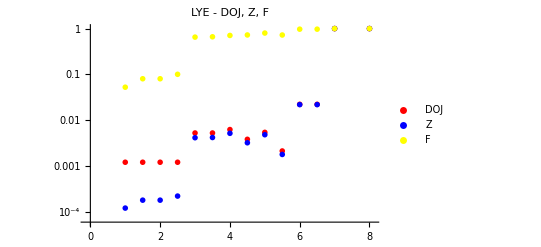

```mathematica
PlotAllParts=ListLogPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotRange->{{-0.1,8.1},All},PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"LYE - DOJ, Z, F", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/LYE/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"LYE_DOJ.txt"]
Put[Union[zPAR,zPBR],"LYE_Z.txt"]
Put[Union[fPAR,fPBR],"LYE_F.txt"]
Export["LYE.jpeg",PlotAllParts,ImageSize->800, ImageResolution->300]
```

LYE.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{-0.001, 0.02},  PlotLabel->"LYE - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["LYE_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```